```mathematica
data=Import["/home/moritz/Dropbox/BenMoritz/FP2/0427-Z0/data/ee.txt","Table"];
```

```mathematica
dataT=Transpose[data];
dataT[[4]]=If[#<150,#,150]&/@dataT[[4]];
names={"run","event","ncharged","pcharged","e_ecal","e_hcal","e_lep","cos_thru","cos_thet"};
```

```mathematica
Dimensions[dataT]
data[[1]]
dataT[[9,1;;10]]
```

{9,93802}

{1308.,1.,2.,81.3279,88.9296,0.,45.639,999.,-0.855789}

{-0.855789,-0.360372,999.,0.395415,999.,999.,0.580949,0.748497,999.,0.136876}

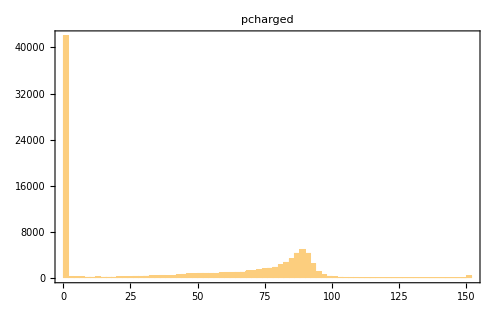

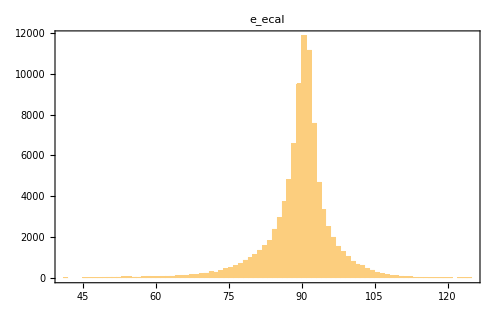

```mathematica
n=4;
Histogram[dataT[[n]],100,PlotRange->{All,All},PlotLabel->names[[n]],Frame->True,ImageSize->500]
n=5;
Histogram[dataT[[n]],100,PlotRange->{All,All},PlotLabel->names[[n]],Frame->True,ImageSize->500]
```

```mathematica
Histogram3D[Transpose[{dataT[[4]],dataT[[5]]}],{200,200},PlotRange->{{0,150},{0,150},All},ImageSize->700,AxesLabel->{"pcharged","e_ecal"},AxesOrigin->{0,0,0}]
```

-Graphics3D-